# BTC dollar cost averaging

```mathematica
(*Buttons to hide/show code*)CloseAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->False]&/@cells;];

OpenAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->True]&/@cells;];

Row[{Button["Hide Code",SelectionEvaluate[CloseAllInputsCells[]]],Button["Show Code",SelectionEvaluate[OpenAllInputsCells[]]]}]
```

Hide CodeShow Code

```mathematica
Clear["Global`"];
SetDirectory[NotebookDirectory[]];
(* Function shortcuts *)
st=StringTemplate;
dollar[a_]:=st["$``"][NumberForm[a,DigitBlock->3]];
(* Default properties for generated plots *)
imagesize=1000;
imagemargins=20;
labelstyle=Directive[14];
titlestyle={20,Red};
subtitlestyle = {15};
imagemargins=20;
plotbackground=Lighter[LightGray,0.75];
updatedstr=Style[st["(updated: ``)"][DateString[]],subtitlestyle];

maniprange=Join[{1,2,3, 6, 9},Range[12,144,6]]//Reverse;
origindate="Sep. 14, 2011";
purchcost=0.03;
btcusd =FinancialData["BTC/USD",origindate];
nbtcusd=btcusd//Normal;
currentprice=Last[Last[nbtcusd]];
dca=<|date->#[[1]],price->#[[2]],infl->InflationAdjust[Quantity[1,DatedUnit["USDollars",#[[1]]]]],sats->IntegerPart[100000000*(1-purchcost)/#[[2]]]|>&/@nbtcusd;
cums=(MapIndexed[#1/#2&,Map[#1[sats]& , Reverse[dca]]//Flatten//N//Accumulate]//Flatten)*currentprice/100000000//Reverse;
dca[[All,"dcaperf"]]=cums;
pv[days_]:=(((#[sats]&/@(Take[dca,-days]))//Total)*currentprice/100000000)/days;
plotlabelstyles={20,16,14};
```

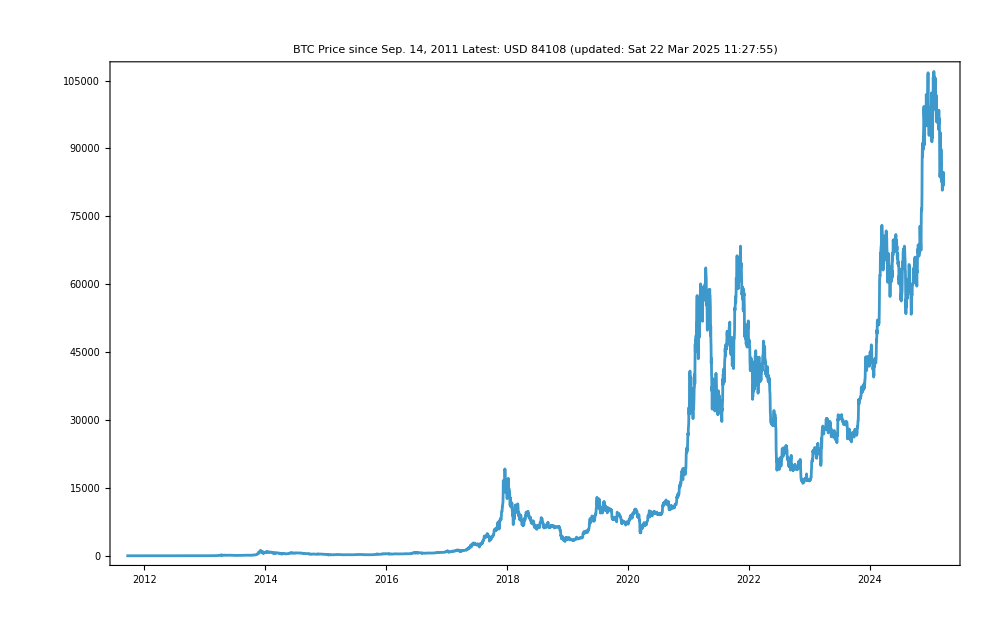

```mathematica
DateListPlot[
btcusd
,ImageSize->imagesize
,GridLines->Automatic
,PlotLabel->Column[
{
Style[
"BTC Price since " <> origindate 
,titlestyle
]
,Style[
"Latest: USD " <> ToString[btcusd["LastValue"]//Round]
,subtitlestyle
]
,updatedstr
}
,Center
]
]
```

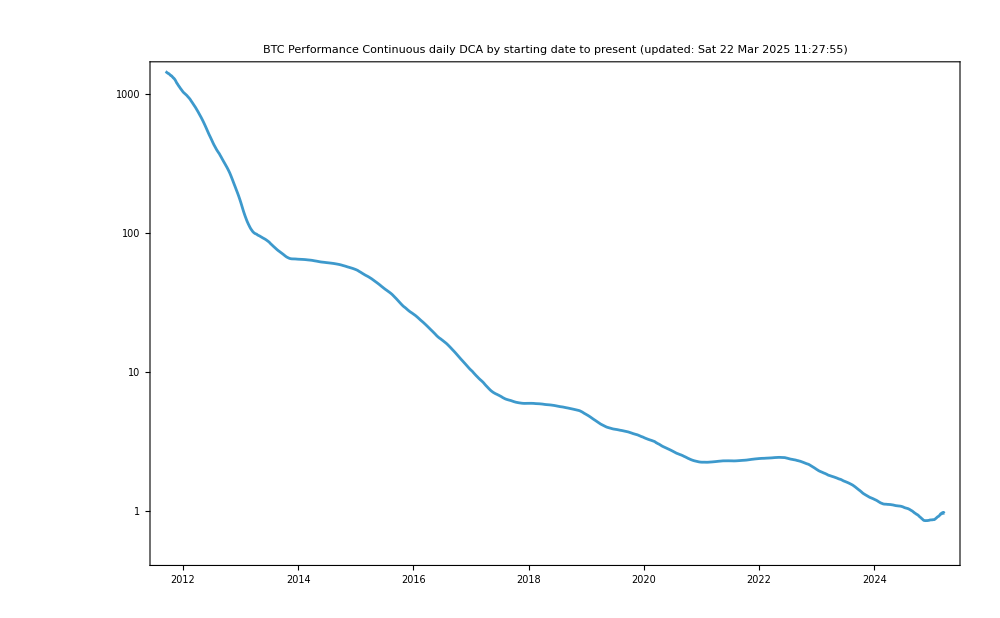

```mathematica
btcdcaperformance=DateListLogPlot[
{#[date],#["dcaperf"]}&/@dca
,GridLines->{Automatic,Join[Range[10],Range[20,100,10],Range[200,10000,100]]}
,ImageSize->imagesize
,ImageMargins->imagemargins
, PlotLabel->Column[{
Style["BTC Performance", titlestyle]
, Style["Continuous daily DCA by starting date to present",subtitlestyle]
,updatedstr
}
,Center
]
];
filename = "BTC-DCA-Performance.jpg";
Export[filename,btcdcaperformance];
btcdcaperformance
```

```mathematica
maniprange=Join[
MapIndexed[#->ToString[First[#2]]<>" mo"&,{1,2,3, 6, 9}]
,MapIndexed[#->ToString[N[#1/12]]<>" yr"&,Range[12,144,6]]
]//Reverse;
ts={#[date],#["dcaperf"]}&/@ dca//TimeSeries;
Manipulate[
Module[{tsx},(
tsx=TimeSeriesWindow[ts,{Today-Quantity[x,"Months"],Today}];
DateListLogPlot[
tsx
,GridLines->{Automatic, Range[0,10,0.1]}
,ImageSize->imagesize
,PlotLabel->Column[
{
Style[
"Cumulative Daily DCA Performance"
,titlestyle
]
,updatedstr
},
Center
]
]
)]
, {
{x, 60, Style["Starting...back",16]}
, maniprange
}
]
```